## Import data files and create interpolation objects

Form factors  span the range q = 1 to 2000 keV and E = 1 eV to 2 keV. 
q is the momentum transfer and E is the electron kinetic energy.
Data is optimised for q = 1 to 500 keV and E = 1 eV to 1 keV. 
Interpolation outside this range is less accurate.

```mathematica
SetDirectory[NotebookDirectory[]];
LCH41agrid=Import["CH4_1a_grid.dat"];
LCH42agrid=Import["CH4_2a_grid.dat"];
LCH42txgrid=Import["CH4_2tx_grid.dat"];
LCH42tygrid=Import["CH4_2ty_grid.dat"];
LCH42tzgrid=Import["CH4_2tz_grid.dat"];
ResetDirectory[];

fCH41a=Interpolation[LCH41agrid,InterpolationOrder->1]
fCH42a=Interpolation[LCH42agrid,InterpolationOrder->1]
fCH42tx=Interpolation[LCH42txgrid,InterpolationOrder->1]
fCH42ty=Interpolation[LCH42tygrid,InterpolationOrder->1]
fCH42tz=Interpolation[LCH42tzgrid,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«2 more identical outputs»

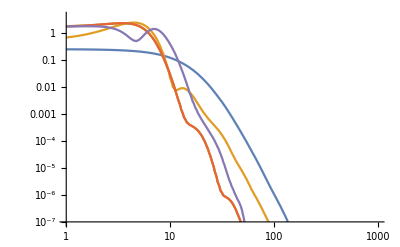

```mathematica
Etest=0.025;

LogLogPlot[{fCH41a[q,Etest],fCH42a[q,Etest],fCH42tx[q,Etest],fCH42ty[q,Etest],fCH42tz[q,Etest]},{q,1,200},PlotRange->{{1,1000},{10^-7,4}}]
```

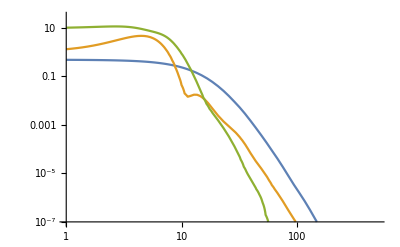

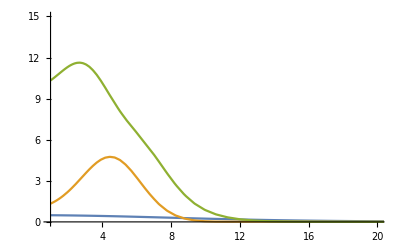

```mathematica
fCH42tave[q1_,E1_]:=1/3(fCH42tx[q1,E1]+fCH42ty[q1,E1]+fCH42tz[q1,E1])

LogLogPlot[{2fCH41a[q,Etest],2fCH42a[q,Etest],6fCH42tave[q,Etest]},{q,1,200},PlotRange->{{1,500},{10^-7,30}}]

Plot[{2fCH41a[q,Etest],2fCH42a[q,Etest],6fCH42tave[q,Etest]},{q,1,200},PlotRange->{{1,20},{0,15}}]
```